```mathematica
Corr1[f0_,fc_,α_,t_]:=NIntegrate[(f0/f)^α Cos[f t],{f,fc,∞}]/ Pi
```

```mathematica
Corr2[f0_,fc_,α_,t_]:=Re[ Gamma[1-α, I fc t] Exp[-I (Pi/2) (1-α)] ] (f0 t)^α / (Pi t)
```

NIntegrate::precw: The precision of the argument function (Cos[2.002 f]/f^2) is less than WorkingPrecision (20.).

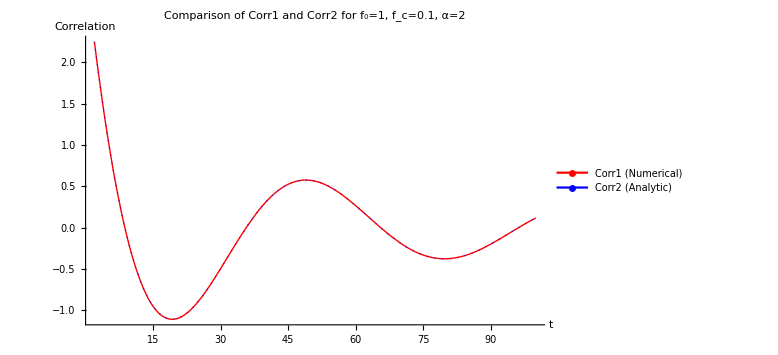

```mathematica
(*Parameters*)f0=1;
fc=0.1;
α=2;

(*Define the functions*)
Corr1[f0_,fc_,α_,t_]:=NIntegrate[(f0/f)^α Cos[f t],{f,fc,∞},MaxRecursion->30,Method->"GlobalAdaptive",WorkingPrecision->20]/Pi

Corr2[f0_,fc_,α_,t_]:=Re[Gamma[1-α,I fc t] Exp[-I (Pi/2) (1-α)]] (f0 t)^α/(Pi t)

(*Plot range and domain*)
tmin=2;
tmax=100;

Plot[{Corr1[f0,fc,α,t],Corr2[f0,fc,α,t]},{t,tmin,tmax},PlotStyle->{{Red,Thick},(*Corr1:Red dashed line*){Blue,Thick,Dotted}       (*Corr2:Blue dotted line*)},PlotLegends->{Placed[LineLegend[{Red,Blue},{"Corr1 (Numerical)","Corr2 (Analytic)"},LegendMarkers->{"-",":"}],Below]},AxesLabel->{"t","Correlation"},PlotLabel->"Comparison of Corr1 and Corr2 for f₀="<>ToString[f0]<>", f_c="<>ToString[fc]<>", α="<>ToString[α],ImageSize->Large]
```

```mathematica
PSD_num[f0_,fc_,α_,f_]
```

```mathematica
(*Parameters*)
f0=1;
fc=0.1;
α=2;Corr2Func[t_]:=Re[Gamma[1-α,I fc t] Exp[-I (Pi/2) (1-α)]] (f0 t)^α/(Pi t)

(*Sampling parameters*)
tmax=1000;
dt=2;
tlist=Range[dt,tmax,dt];
n=Length[tlist];

(*Sampled data*)
corrSamples=Table[Corr2Func[t],{t,tlist}];

(*Apply Fourier transform:we use Fourier with proper scaling*)
ftData=Fourier[corrSamples,FourierParameters->{1,-1}];

(*Frequency axis (FFT frequencies)*)
df=1/(n dt);  (*frequency resolution*)
frequencies=Table[(k-1) df,{k,n}];

(*Optional:Shift zero frequency to center (for display symmetry)*)
ftShifted=FourierShift[ftData];
freqShifted=FourierShift[frequencies];

(*Plot magnitude of FT*)
ListLinePlot[Transpose[{freqShifted,Abs[ftShifted]}],PlotRange->All,PlotLabel->"Numerical Fourier Transform of Corr2(t)",AxesLabel->{"f","|Corr2̃(f)|"},PlotStyle->Blue,ImageSize->Large]
```

-Graphics-